```mathematica
<<ProbabilisticBricks`
```

```mathematica
setProblemProperties[81,40,2,1,0.1,0.7];
```

```mathematica
generateContacts[];
```

```mathematica
p=Table[{0,0,1,0,0,0},{nelx}];
p[[IntegerPart[nelx/2]+1]]={0,0,10,5,0,0};
p=Flatten[p];
setBoundaryConditions[p];
```

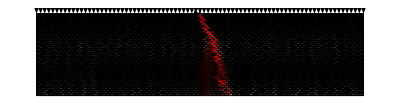

```mathematica
solveProblem[]
displayWallWithFilter["stress_state"]
```

```mathematica
eqCheck
```

True

```mathematica
Hu=Import["collapse_data_80x40.m"];
```

```mathematica
nTests=300;
(*Hu={};*)
For[n=1,n≤nTests,n++,
generateContacts[];
eqCheck=True;
H1=10;H2=40.;f=False;
While[!f,
H=(H1+H2)/2;
p=Table[{0,0,1,0,0,0},{nelx}];
p[[IntegerPart[nelx/2]+1]]={0,0,10,H,0,0};
p=Flatten[p];
setBoundaryConditions[p];
solveProblem[];
If[Abs[H1-H2]<.1,
AppendTo[Hu,H];
f=True;,
If[eqCheck,
H1=H;,
H2=H;
];
];
];
];
Hu;
```

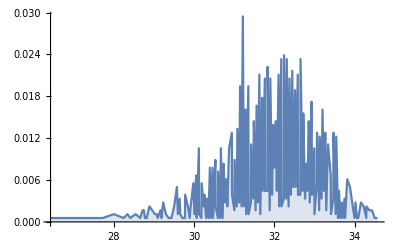

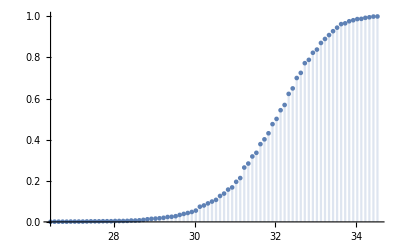

```mathematica
dist=EmpiricalDistribution[Hu];
DiscretePlot[PDF[dist,x],{x,Hu}]
DiscretePlot[CDF[dist,x],{x,Min[Hu],Max[Hu],.1}]
```

```mathematica
{Mean[dist],Quantile[dist,0.05],StandardDeviation[dist],StandardDeviation[dist]/Mean[dist]}
```

{31.9081,29.9854,1.13467,0.0355606}

```mathematica
Length[Hu]
```

1800

```mathematica
Export["collapse_data_80x40.m",Hu]
```

collapse_data_80x40.m